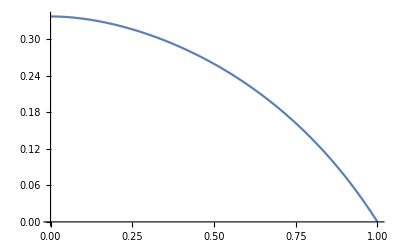

-Graphics-

1/6 λ (6+3 λ-4 λ^2)

1/6 λ (30+15 λ-8 λ^2)

1/6 λ (-6-3 λ+16 λ^2)

```mathematica
δ=0.0495092; (*rad*)
γ=29.3;
ϕ=Pi/2;
d=((1-λ)(2λ+1)Sin[ϕ]Sin[δ])/(γ((5+5λ-4λ^2)+(8λ^2-λ-1)Cos[ϕ]))*10^3;
Plot[d, {λ,0,1}]
FullSimplify[%]
A1=Simplify[Integrate[(1-λ)(2λ+1),λ]]
A2=Simplify[Integrate[(5+5λ-4λ^2),λ]]
A3=Simplify[Integrate[8λ^2-λ-1,λ]]
(*CForm[A1]*)
(*CForm[A2]
CForm[A3]*)
```

```mathematica
1/6 λ (-6-3 λ+16 λ^2)
```